```mathematica
Lx=10*10^-3;Ly=3*10^-3;Lz=25*10^-3;M=8.7*10^5;μ=4π*10^-7;
B`single`magnet`x[x_,y_,z_,Mx_,My_,Mz_]:=10000*μ*M/(4π)*Sum[(-1)^(k+l+m)*Log[(z-Mz)+(-1)^m(Lz/2)+√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2)],{k,1,2},{l,1,2},{m,1,2}];
B`single`magnet`y0[x_,y_,z_,Mx_,My_,Mz_]:=10000*μ*-M/(4π)*Sum[(-1)^(k+l+m)*(((y-My)+(-1)^l(Ly/2))((x-Mx)+(-1)^k(Lx/2)))/(Abs[(y-My)+(-1)^l(Ly/2)]*Abs[(x-Mx)+(-1)^k(Lx/2)])*ArcTan[(Abs[(x-Mx)+(-1)^k(Lx/2)]*((z-Mz)+(-1)^m(Lz/2)))/(Abs[(y-My)+(-1)^l(Ly/2)]*√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2))],{k,1,2},{l,1,2},{m,1,2}];
B`single`magnet`y[x_,y_,z_,Mx_,My_,Mz_]:=If[Abs[y-My]≤Ly/2&&Abs[x-Mx]≤Lx/2&&Abs[z-Mz]≤Lz/2,-B`single`magnet`y0[x,y,z,Mx,My,Mz],B`single`magnet`y0[x,y,z,Mx,My,Mz]];
B`single`magnet`z[x_,y_,z_,Mx_,My_,Mz_]:=10000*μ*M/(4π)*Sum[(-1)^(k+l+m)*Log[(x-Mx)+(-1)^k(Lx/2)+√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2)],{k,1,2},{l,1,2},{m,1,2}];

BSX[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[B`single`magnet`x[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BSY[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[B`single`magnet`y[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BSZ[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[B`single`magnet`z[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BS[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sqrt[BSX[x,y,z,Xstack,Ystack,Zstack]^2+BSY[x,y,z,Xstack,Ystack,Zstack]^2+BSZ[x,y,z,Xstack,Ystack,Zstack]^2];
```

```mathematica
B`single`magnet`y[0,0,0,0,0,0]
```

8745.

```mathematica
stackposition1={37,0,49}*10^-3;
stackposition2={37,0,-49}*10^-3;
stackposition3={-37,0,49}*10^-3;
stackposition4={-37,0,-49}*10^-3;
```

177.917

179.962

175.872

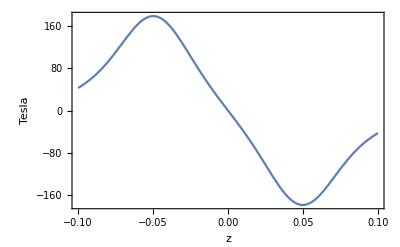

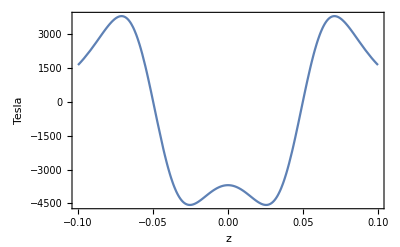

```mathematica
BYcentral[z_]:=-BSY[0,0,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,0,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,0,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,0,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
len=2000;δz=0.2/len;z0=-0.1;
dataB=Table[{z0+i*δz,BYcentral[z0+i*δz]},{i,0,len}];
max`value1=Max[dataB[[All,2]]](*For M=8.7*10^5*)
max`value2=max`value1*8.8/8.7
max`value3=max`value1*8.6/8.7
(*data∇B=Table[{z0+i*δz,(BYcentral[z0+(i+1)*δz]-BYcentral[z0+i*δz])/δz},{i,0,len}];*)
BYcc=Interpolation@dataB;
(*gradient=Interpolation@data∇B;*)
Plot[BYcc[z],{z,-0.1,0.1},Frame->True,FrameLabel->{"z","Tesla"}]
Plot[BYcc'[z],{z,-0.1,0.1},Frame->True,FrameLabel->{"z","Tesla"}]
```

```mathematica
StreamDensityPlot[{-BSY[0,y,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,y,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,y,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,y,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]],-BSZ[0,y,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]+-BSZ[0,y,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSZ[0,y,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSZ[0,y,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]]},{y,-100,100},{z,-100,100}]
```

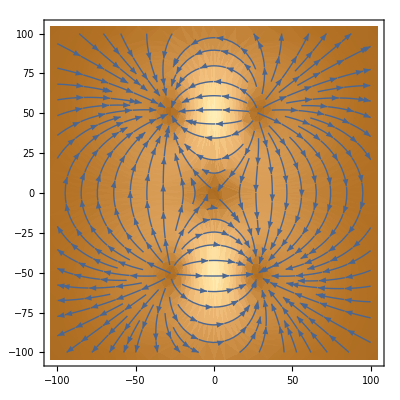

0.0067356

0.00681302

0.00665818

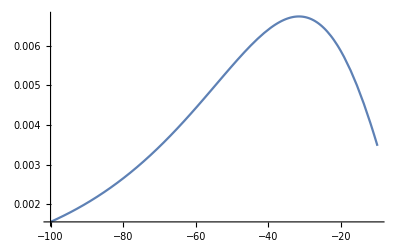

```mathematica
BYcentral[y_]:=-BSY[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
BXcentral[y_]:=-BSX[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSX[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSX[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSX[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
BZcentral[y_]:=-BSZ[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSZ[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSZ[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSZ[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
Bmagnitude[y_]:=Sqrt[BXcentral[y]^2+BYcentral[y]^2+BZcentral[y]^2];
leny=2000;δy=0.09/leny;y0=-0.1;
datamagnitude=Table[{y0+i*δy,Bmagnitude[y0+i*δy]},{i,0,leny}];
Max`value1=Max[datamagnitude[[All,2]]](*For M=8.7*10^5*)
Max`value2=Max`value1*8.8/8.7(*For M=8.8*10^5*)
Max`value3=Max`value1*8.6/8.7(*M=8.6*10^5*)
BMa=Interpolation@datamagnitude;
Plot[BMa[y],{y,-0.1,-0.01}]
```

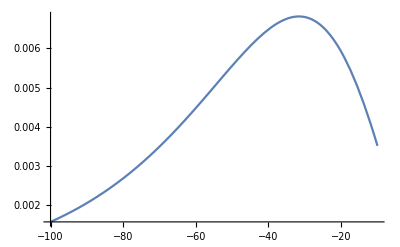

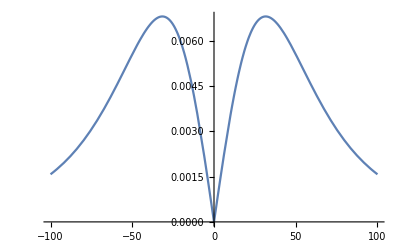

```mathematica
Plot[Bmagnitude[y],{y,-0.1,0.1}]
```

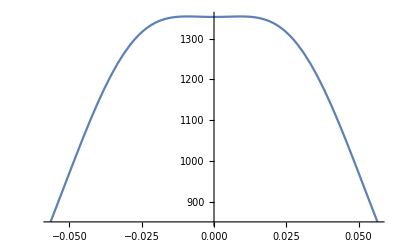

```mathematica
μ=4π*10^-7;A=400;(*L`solenoid=0.02;*)d`outer=4.7625*10^-3;d`copper=3*10^-3;
r1=3.75*10^-2;r2=6.1*10^-2;r3=8.5*10^-2;distance=3.75*10^-2+4*d`outer;n=4;
R1=r1+(d`outer)/2;R2=r2+(d`outer)/2;
gap`inner=(r2-r1-d`outer)/2;gap`outer=(r3-r2-d`outer)/2;
sincoil[r_,y_,poc_]:=10000*(μ*A)/2*r^2/((r^2+(y-poc)^2)^(3/2));
(*solenoid[r_,y_]:=n*sincoil[r,y,0];*)
solenoid[r_,y_]:=Sum[sincoil[r,y,i*d`outer],{i,{-2,-1,1,2}}];
solenoid3[r_,y_]:=Sum[sincoil[r,y,i*d`outer],{i,{-1,0,1}}];
B`inner[y_]:=Sum[solenoid[R1+i*gap`inner,distance/2+y]+solenoid[R1+i*gap`inner,y-distance/2],{i,0,1}]+solenoid3[R1+2*gap`inner,distance/2+y]+solenoid3[R1+2*gap`inner,y-distance/2];
B`outer[y_]:=Sum[solenoid[R2+i*gap`outer,distance/2+y]+solenoid[R2+i*gap`outer,y-distance/2],{i,0,1}]+solenoid3[R2+2*gap`outer,distance/2+y]+solenoid3[R2+2*gap`outer,y-distance/2];
(*B`inner[y_]:=solenoid[(r1+r2)/2,distance/2+y]+solenoid[(r1+r2)/2,y-distance/2];
B`outer[y_]:=solenoid[(r2+r3)/2,distance/2+y]+solenoid[(r2+r3)/2,y-distance/2];*)
B`total[y_]:=(B`inner[y]+B`outer[y]);
Plot[B`total[y],{y,-distance,distance}]
```

```mathematica
(*=====================================================+++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*μ=4π*10^-7;A=400;(*L`solenoid=0.02;*)d`outer=4.7625*10^-3;d`copper=3*10^-3;                                   (**)
r1=3.75*10^-2;r2=6.1*10^-2;r3=8.5*10^-2;                                                                         
distance=5.75*10^-2;n=4;                                                 
R1=r1+(d`outer)/2;R2=r2+(d`outer)/2;
gap`inner=(r2-r1-d`outer)/2;gap`outer=(r3-r2-d`outer)/2;
S4[r_,y_]:=10000*(4*μ*A)/2*(r^2/((r^2+(y-distance/2)^2)^(3/2))+r^2/((r^2+(y+distance/2)^2)^(3/2)));       (*Directly solution no care the size*)
S3[r_,y_]:=10000*(3*μ*A)/2*(r^2/((r^2+(y-distance/2)^2)^(3/2))+r^2/((r^2+(y+distance/2)^2)^(3/2)));
B1[y_]:=Sum[S4[R1+i*gap`inner,y],{i,0,1}]+S3[R1+2*gap`inner,y];
B2[y_]:=Sum[S4[R2+i*gap`inner,y],{i,0,1}]+S3[R2+2*gap`inner,y];
B1[0]/A*)                                                                                                                                                                                                                                 (**)
(*=====================================================+++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
```

```mathematica
B`one`magnets`y[x_,y_,z_,TwY_]:=Sum[B`single`magnet`y[x,y,z,0,TwY+i*Ly,0],{i,0,0}];
B`two`magnets`y[x_,y_,z_,TwY_]:=Sum[B`single`magnet`y[x,y,z,0,TwY+i*Ly,0],{i,-1,1,1}];
L=0.5*10^-3;
```

```mathematica
Manipulate[pm=pm/.First@FindRoot[B`one`magnets`y[0,0,0,pm]-B`two`magnets`y[0,0,0,pm+d]==-0.01,{pm,0.1,0.1,20distance}];
fig2=Plot[{B`total[y]+B`one`magnets`y[0,y,0,pm]-B`two`magnets`y[0,y,0,pm+d],B`total[y],B`one`magnets`y[0,y,0,pm]-B`two`magnets`y[0,y,0,pm+d]},{y,distance/2,pm},PlotLegends->{"Total","solenoid","magnet"},PlotStyle->{Dashed,Red,Blue},ImageSize->Medium];
py=py/.First@FindRoot[B`total[py]+B`one`magnets`y[0,py,0,pm]-B`two`magnets`y[0,py,0,pm+d]==0,{py,distance}];
fig3=Plot[B`total[y]+B`one`magnets`y[0,y,0,pm]-B`two`magnets`y[0,y,0,pm+d],{y,py-L/2,py+L/2},ImageSize->Medium];
slope=((B`total[py-L/2]+B`one`magnets`y[0,py-L/2,0,pm]-B`two`magnets`y[0,py-L/2,0,pm+d])-(B`total[py+L/2]+B`one`magnets`y[0,py+L/2,0,pm]-B`two`magnets`y[0,py+L/2,0,pm+d]))/L;
Grid[{{pm,py,slope},{fig2,fig3}}],
{d,Ly,10*Ly}]
```

0.507112

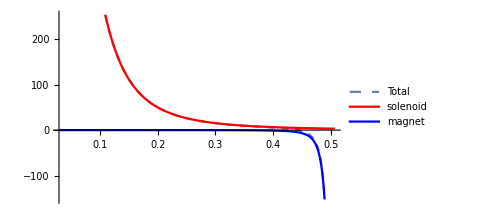

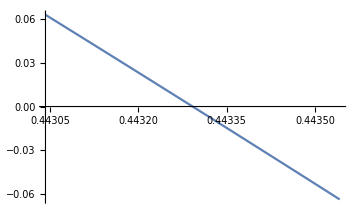

252.24

0.6

```mathematica
pm=pm/.First@FindRoot[-B`one`magnets`y[0,0,0,pm]==-0.01,{pm,0.1,0.1,20distance}]
Plot[{B`total[y]-B`one`magnets`y[0,y,0,pm],B`total[y],-B`one`magnets`y[0,y,0,pm]},{y,distance/2,pm},PlotLegends->{"Total","solenoid","magnet"},PlotStyle->{Dashed,Red,Blue},ImageSize->Medium]
py=py/.First@FindRoot[B`total[py]-B`one`magnets`y[0,py,0,pm]==0,{py,distance}];
fig3=Plot[B`total[y]-B`one`magnets`y[0,y,0,pm],{y,py-L/2,py+L/2},ImageSize->Medium]
slope=((B`total[py-L/2]-B`one`magnets`y[0,py-L/2,0,pm])-(B`total[py+L/2]-B`one`magnets`y[0,py+L/2,0,pm]))/L
```

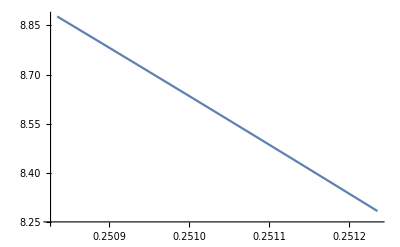

0.593467

-1483.59

```mathematica
y0=py;δy=0.05*10^-3;
data=Table[{y0+i*δy,B`total[y0+i*δy]-B`one`magnets`y[0,y0+i*δy,0,pm]},{i,-4,4}];
ListLinePlot@data
dif=Max@data[[All,2]]-Min@data[[All,2]]
fun=Interpolation@data;
slope=fun'[py]
```

```mathematica
(*Sensor coefficient*)
L`sensor=0.5*10^-3;
standard=60*10^-6*10^4//N
```

```mathematica
(*μ=4π*10^-7;A=400;r1=3.75*10^-2;r2=6.1*10^-2;r3=8.5*10^-2;distance=5.75*10^-2;n=4;
d`outer=4.7625*10^-3;d`copper=3*10^-3;R1=r1+(d`outer)/2;R2=r2+(d`outer)/2;gap`inner=(r2-r1-d`outer)/2;gap`outer=(r3-r2-d`outer)/2;
single`x[r_,x_,y_,z_,poc_]:=(μ*A*r)/(4π)*NIntegrate[(Sin[θ]*(y-poc))/(((z-r*Cos[θ])^2+(x-r*Sin[θ])^2+(y-poc)^2)^(3/2)),{θ,0,2π}];
single`y[r_,x_,y_,z_,poc_]:=(μ*A*r)/(4π)*NIntegrate[(r-z*Cos[θ]-x*Sin[θ])/(((z-r*Cos[θ])^2+(x-r*Sin[θ])^2+(y-poc)^2)^(3/2)),{θ,0,2π}];
single`z[r_,x_,y_,z_,poc_]:=(μ*A*r)/(4π)*NIntegrate[(Cos[θ]*(y-poc))/(((z-r*Cos[θ])^2+(x-r*Sin[θ])^2+(y-poc)^2)^(3/2)),{θ,0,2π}];
solenoid`x[r_,x_,y_,z_]:=Sum[single`x[r,x,y,z,i*d`outer],{i,{-2,-1,1,2}}];
solenoid`y[r_,x_,y_,z_]:=Sum[single`y[r,x,y,z,i*d`outer],{i,{-2,-1,1,2}}];
solenoid`z[r_,x_,y_,z_]:=Sum[single`z[r,x,y,z,i*d`outer],{i,{-2,-1,1,2}}];
solenoid3`x[r_,x_,y_,z_]:=Sum[single`x[r,x,y,z,i*d`outer],{i,{-1,0,1}}];
solenoid3`y[r_,x_,y_,z_]:=Sum[single`y[r,x,y,z,i*d`outer],{i,{-1,0,1}}];
solenoid3`z[r_,x_,y_,z_]:=Sum[single`z[r,x,y,z,i*d`outer],{i,{-1,0,1}}];
B`inner`x[x_,y_,z_]:=Sum[solenoid`x[R1+i*gap`inner,x,distance/2+y,z]+solenoid`x[R1+i*gap`inner,x,y-distance/2,z],{i,0,1}]+solenoid3`x[R1+2*gap`inner,x,distance/2+y,z]+solenoid3`x[R1+2*gap`inner,x,y-distance/2,z];
B`inner`y[x_,y_,z_]:=Sum[solenoid`y[R1+i*gap`inner,x,distance/2+y,z]+solenoid`y[R1+i*gap`inner,x,y-distance/2,z],{i,0,1}]+solenoid3`y[R1+2*gap`inner,x,distance/2+y,z]+solenoid3`y[R1+2*gap`inner,x,y-distance/2,z];
B`inner`z[x_,y_,z_]:=Sum[solenoid`z[R1+i*gap`inner,x,distance/2+y,z]+solenoid`z[R1+i*gap`inner,x,y-distance/2,z],{i,0,1}]+solenoid3`z[R1+2*gap`inner,x,distance/2+y,z]+solenoid3`z[R1+2*gap`inner,x,y-distance/2,z];
(*=====+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++===================================*)
B`outer`x[x_,y_,z_]:=Sum[solenoid`x[R2+i*gap`outer,x,distance/2+y,z]+solenoid`x[R2+i*gap`outer,x,y-distance/2,z],{i,0,1}]+solenoid3`x[R2+2*gap`outer,x,distance/2+y,z]+solenoid3`x[R2+2*gap`outer,x,y-distance/2,z];
B`outer`y[x_,y_,z_]:=Sum[solenoid`y[R2+i*gap`outer,x,distance/2+y,z]+solenoid`y[R2+i*gap`outer,x,y-distance/2,z],{i,0,1}]+solenoid3`y[R2+2*gap`outer,x,distance/2+y,z]+solenoid3`y[R2+2*gap`outer,x,y-distance/2,z];
B`outer`z[x_,y_,z_]:=Sum[solenoid`z[R2+i*gap`outer,x,distance/2+y,z]+solenoid`z[R2+i*gap`outer,x,y-distance/2,z],{i,0,1}]+solenoid3`z[R2+2*gap`outer,x,distance/2+y,z]+solenoid3`z[R2+2*gap`outer,x,y-distance/2,z];
B`total`x[x_,y_,z_]:=B`inner`x[x,y,z]+B`outer`x[x,y,z];
B`total`y[x_,y_,z_]:=B`inner`y[x,y,z]+B`outer`y[x,y,z];
B`total`z[x_,y_,z_]:=B`inner`z[x,y,z]+B`outer`z[x,y,z];*)
```

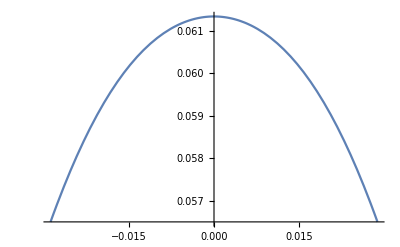

```mathematica
Plot[B`outer`y[0,y,0],{y,-distance/2,distance/2}]
```

```mathematica
B`outer`y[0,0,0]/A
```

```mathematica
Clear["Global`*"]
```

Plot::plln: Limiting value -0.0005+(0.206484/.45.4436-If[«3»]-If[«3»]==0/.-If[LessEqual[«2»],Times[«2»],B`single`magnet`y0[«6»]]-If[LessEqual[«2»],Times[«2»],B`single`magnet`y0[«6»]]+0.0039974/Plus[«2»]^(3/2)+0.0060961/Plus[«2»]^(3/2)+0.0100963/Plus[«2»]^(3/2)+0.0133932/Plus[«2»]^(3/2)+«35»+0.0171553/Plus[«2»]^(3/2)+0.0039974/Plus[«2»]^(3/2)+0.0060961/Plus[«2»]^(3/2)+0.0100963/Plus[«2»]^(3/2)+0.0133932/Plus[«2»]^(3/2)==0/.«1»==0/.«1»==0) in {y,-0.0005+(«1»),0.0005+(0.206484/.45.4436+Times[«2»]+Times[«2»]==0/.-If[«3»]-If[«3»]+0.0039974 Power[«2»]+0.0060961 Power[«2»]+0.0100963 Power[«2»]+0.0133932 Power[«2»]+0.0039974 Power[«2»]+«32»+0.0100963 Power[«2»]+0.0133932 Power[«2»]+0.0171553 Power[«2»]+0.0039974 Power[«2»]+0.0060961 Power[«2»]+0.0100963 Power[«2»]+0.0133932 Power[«2»]==0/.«1»==0/.«46»+(«21»)/(«1»)==0)} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

ReplaceAll::reps: {-If[Abs[Plus[«2»]]≤3/2000,-B`single`magnet`y0[0,0,0,0,Plus[«2»],0],B`single`magnet`y0[0,0,0,0,3/500+ReplaceAll[«2»],0]]-If[Abs[Plus[«2»]]≤3/2000,-B`single`magnet`y0[0,0,0,0,Plus[«2»],0],B`single`magnet`y0[0,0,0,0,3/1000+ReplaceAll[«2»],0]]-If[Abs[ReplaceAll[«2»]]≤3/2000,-B`single`magnet`y0[0,0,0,0,ReplaceAll[«2»],0],B`single`magnet`y0[0,0,0,0,ReplaceAll[«2»]/.Equal[«2»],0]]+B`one`magnet`y[0,0,0,ReplaceAll[«2»]/.Equal[«2»]/.Plus[«4»]==-0.1/.Times[«2»]+Times[«2»]+Times[«2»]+B`one`magnet`y[«4»]==-0.1]==-0.1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.154738+B`one`magnet`y[0.,0.,0.,0.,0.29041,0.]==-0.1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«48»+0.0133932/((«21»+(«1»)^2)^(3/2))+B`one`magnet`y[0,y,0,ReplaceAll[«2»]/.Equal[«2»]/.Plus[«4»]==-0.1/.Times[«2»]+Times[«2»]+Times[«2»]+B`one`magnet`y[«4»]==-0.1]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.